```mathematica
f[x_]:=(7x+2)/4+(-2-5x)/4 Cos[x π]
```

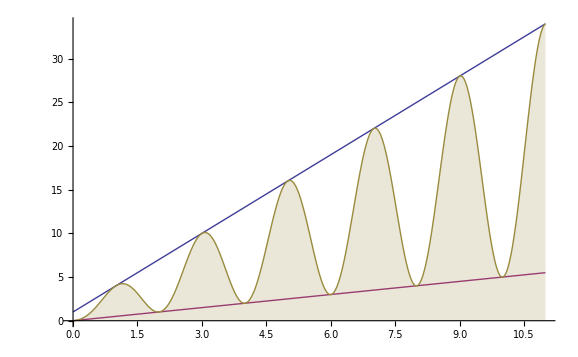

```mathematica
l=0;r=11;
Plot[{3x+1,x/2,f[x]},{x,l,r},Filling->{3->Bottom},PlotRange->{{l,r},{0,f[If[Mod[r,2]==0,r-1,r]]}}]
```

```mathematica
Manipulate[Try=(f[a x+b]-b)/a//Simplify;
Plot[{Try,x},{x,0,50},PlotRange->Full,PlotLabel->Try],{{a,0.25},-10,10},{{b,0},-10,10}]
```

```mathematica
g[n_,a_,b_,m_]:=If[Mod[n,m],n/m,a n+b];
```

```mathematica
h=If[#1==1,{},{{#1,f[#1]}}∪#0[f[#1]]]&
```

If[#1==1,{},{{#1,f[#1]}}∪#0[f[#1]]]&

```mathematica
h[3]
```

{{2,1},{3,10},{4,2},{5,16},{8,4},{10,5},{16,8}}

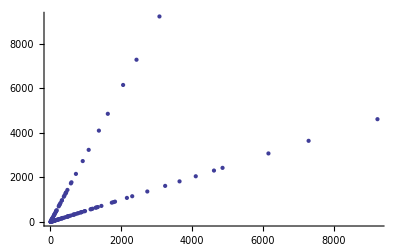

```mathematica
ListPlot[h[27]]
```

```mathematica
diedai=If[#1!=1,{{{#1,f[#1]},{f[#1],f[f[#1]]}}}∪#0[f[#1]],{}]&
```

If[#1≠1,{{{#1,f[#1]},{f[#1],f[f[#1]]}}}∪#0[f[#1]],{}]&

```mathematica
diedai[7]
```

{{{2,1},{1,4}},{{4,2},{2,1}},{{5,16},{16,8}},{{7,22},{22,11}},{{8,4},{4,2}},{{10,5},{5,16}},{{11,34},{34,17}},{{13,40},{40,20}},{{16,8},{8,4}},{{17,52},{52,26}},{{20,10},{10,5}},{{22,11},{11,34}},{{26,13},{13,40}},{{34,17},{17,52}},{{40,20},{20,10}},{{52,26},{26,13}}}

```mathematica
dir[n_]:=Module[{A={},m=n,i=1},While[m!=1,A=A∪{{i,{{m,f[m]},{f[m],f[f[m]]}}}};m=f[m];i=i+1];A]
```

```mathematica
dir[7]
dir[7][[All,2]]
dir[n][[1;;2,2]]
```

{{1,{{7,22},{22,11}}},{2,{{22,11},{11,34}}},{3,{{11,34},{34,17}}},{4,{{34,17},{17,52}}},{5,{{17,52},{52,26}}},{6,{{52,26},{26,13}}},{7,{{26,13},{13,40}}},{8,{{13,40},{40,20}}},{9,{{40,20},{20,10}}},{10,{{20,10},{10,5}}},{11,{{10,5},{5,16}}},{12,{{5,16},{16,8}}},{13,{{16,8},{8,4}}},{14,{{8,4},{4,2}}},{15,{{4,2},{2,1}}},{16,{{2,1},{1,4}}}}

{{{7,22},{22,11}},{{22,11},{11,34}},{{11,34},{34,17}},{{34,17},{17,52}},{{17,52},{52,26}},{{52,26},{26,13}},{{26,13},{13,40}},{{13,40},{40,20}},{{40,20},{20,10}},{{20,10},{10,5}},{{10,5},{5,16}},{{5,16},{16,8}},{{16,8},{8,4}},{{8,4},{4,2}},{{4,2},{2,1}},{{2,1},{1,4}}}

Part::take: Cannot take positions 1 through 2 in {}.

{}⟦1;;2,2⟧

```mathematica
Manipulate[ListLinePlot[{{{n,0},{n,f[n]}}}∪dir[n][[1;;i,2]],PlotRange->{{0,Max[dir[n][[All,2]]]},{0,Max[dir[n][[All,2]]]}},PlotStyle->Red,PlotMarkers->Automatic],{i,2,Length[dir[n][[All,2]]],1},{n,3,27,2}]
```

```mathematica
n=41
Manipulate[ListLinePlot[{{{n,0},{n,f[n]}}}∪dir[n][[1;;i,2]],PlotRange->{{0,Max[dir[n][[All,2]]]},{0,Max[dir[n][[All,2]]]}},PlotStyle->Red,PlotMarkers->Automatic],{i,2,Length[dir[n][[All,2]]],1}]
```

41

```mathematica
Manipulate[ListVectorPlot[diedai[n]],{n,3,51,2}]
```

ListVectorPlot::vfldata: diedai[5] is not a valid vector field dataset or a valid list of datasets.

```mathematica
diedai[5]
```

{{{2,1},{1,4}},{{4,2},{2,1}},{{5,16},{16,8}},{{8,4},{4,2}},{{16,8},{8,4}}}

```mathematica
Manipulate[ListVectorPlot[{{{2,1},{1,4}},{{4,2},{2,1}},{{5,16},{16,8}},{{8,4},{4,2}},{{16,8},{8,4}}},VectorPoints->{m,n}],{m,2,20,1},{n,2,20,1}]
```